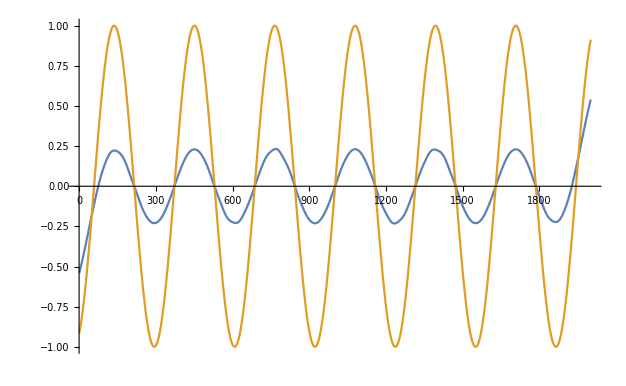

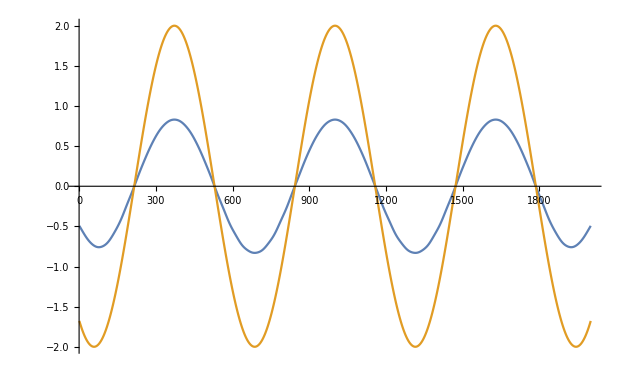

```mathematica
A=1;f=1;
f1[x_]:=A*Cos[2*Pi*f*x];
f2[x_]:=A*Sin[2*Pi*f*x];
s1[x_]:=Sin[2*x];
s2[x_]:=2*Cos[x];
c1[x_]:=Sin[10*x];
res[a_]:=f1[a]*s1[a]+f2[a]*s2[a];

points:=Range[-10,10,.01];
resPoints:=res[points]

f1Points:=f1[points]
s1Points:=s1[points]

f2Points:=f2[points]
s2Points:=s2[points]

ListLinePlot[{LowpassFilter[resPoints*f1Points,.01],s1Points}]
ListLinePlot[{LowpassFilter[resPoints*f2Points,.01],s2Points}]
```